## Section -1

```mathematica
n=50000;mcn=Table[0,{i,11+4}];
man=mcn;man1=mcn;man2=mcn;
```

```mathematica
i=1;
While[i<10,{s1=4+i;cn=ParallelTable[r=s1;a=01;q=20;
(* qt is q^∼ (Majorana mass term), and a is mass term (m) and q is Dirac mass term in cw fermions. *)
ce1[a_,q_]:=RandomReal[{a,a+q},r] ;
ce2[a_,q_]:=RandomReal[{0,q},r] ;
gc = ce1[a,q];(*ce1 diagonal terms*)
hc = ce2[a,q];(*ce2 off-diagonal terms*)
cw2 = Table[0,{x,2r+1},{y,2r+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;While[i<r+1,{cw2[[i,r+i]] = cw2[[r+i,i]] = 0+1.0gc[[i]]};i++];
i=1;While[i<r+1,{cw2[[i,r+1+i]] =cw2[[r+1+i,i]] = -01.0hc[[i]]};i++];
cw2;
cw3 = cw2[[r+1;;2r+1,1;;r]];
cw4=cw3.Transpose[cw3];
cw=cw3//Transpose;
nc=NullSpace[cw];
Min[Abs[nc[[1]]]],{l,n}];
An=ParallelTable[e1[t_,W_]:=RandomReal[{t,t+W},K] ;
e2[t_]:=RandomReal[{0,t},K] ; (* Subscript[e, i] are randomly drawn from limit (2t , 2t+W) *)
t=01;W=20;K=s1; 
(* Attributing values for t , W and K . K is number of fermions. *)
g = e1[t,W];
h = e2[W];
Ox = Table[0,{x,K},{y,K}]; 
(* Defining the dummy matrix to store the values for mass matrix. *)
i=1;While[i<K+1,{Ox[[i,i]] =00.00W+1*g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i]] =Ox[[i,i+1]] =1W/2+00.0/2* h[[i]]};i++];
Ox;
Min[Abs[Eigenvectors[Ox][[-1]]]],{l,n}];
An1=ParallelTable[e1[t_,W_]:=RandomReal[{t,t+W},K] ;
e2[t_]:=RandomReal[{0,t},K] ;(* Subscript[e, i] are randomly drawn from limit (2t , 2t+W) *)
t=01;W=20;K=s1; 
(* Attributing values for t , W and K . K is number of fermions. *)
g = e1[t,W];(*h = e2[t];*)
h = e2[W];
Ox = Table[0,{x,K},{y,K}]; 
(* Defining the dummy matrix to store the values for mass matrix. *)
i=1;While[i<K+1,{Ox[[i,i]] =W/2+0*g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i]] =Ox[[i,i+1]] =0t/2+01* h[[i]]};i++];
Ox;
Min[Abs[Eigenvectors[Ox][[-1]]]],{l,n}];
An2=ParallelTable[e1[t_,W_]:=RandomReal[{t,t+W},K] ;
e2[t_]:=RandomReal[{0,t},K] ; (* Subscript[e, i] are randomly drawn from limit (2t , 2t+W) *)
t=01;W=20;K=s1; 
(* Attributing values for t , W and K . K is number of fermions. *)
g = e1[t,W];
h = e2[W];
Ox = Table[0,{x,K},{y,K}]; 
(* Defining the dummy matrix to store the values for mass matrix. *)
i=1;While[i<K+1,{Ox[[i,i]] =00.00W+1*g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i]] =Ox[[i,i+1]] =0t/2+01* h[[i]]};i++];
Ox;
Min[Abs[Eigenvectors[Ox][[-1]]]],{l,n}];
mcn[[i+4]]=Median[cn];
man[[i+4]]=Median[An];
man1[[i+4]]=Median[An1];
man2[[i+4]]=Median[An2];Print[i]};i++]
```

1

2

3

4

5

6

7

8

9

```mathematica
(*ListLinePlot[{Log10[cn],Log10[An1],Log10[An],Log10[An2]},PlotRange->All,PlotLegends->{"CW 0-mode","Random Site","Random Coupling","Both Random"},Frame->True,FrameLabel->{"Trial Count","Log of |min| of evector's component on a site"}]*)
```

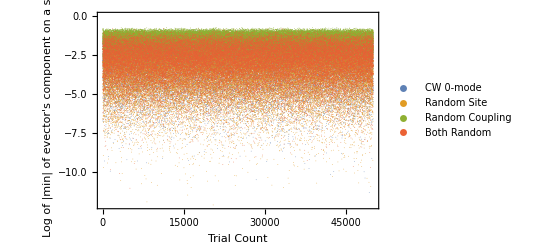

```mathematica
ListPlot[{Log10[cn],Log10[An1],Log10[An],Log10[An2]},PlotRange->All,PlotLegends->{"CW 0-mode","Random Site","Random Coupling","Both Random"},Frame->True,FrameLabel->{"Trial Count","Log of |min| of evector's component on a site"},PlotStyle->PointSize[0.001] (*Adjust the point size here*)]
```

```mathematica
(*Partition the data into chunks of size 10*)
tempcn=Partition[cn,50];
tempan1=Partition[An1,50];
tempan=Partition[An,50];
tempan2=Partition[An2,50];

(*Calculate the median of each chunk*)
medcn=Median/@tempcn;
medan1=Median/@tempan1;
medan=Median/@tempan;
medan2=Median/@tempan2;
```

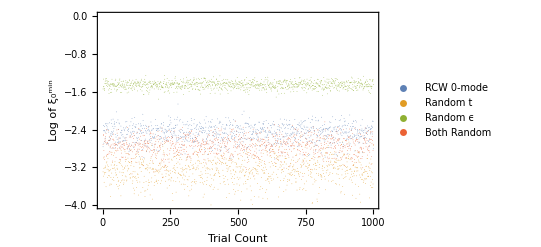

```mathematica
ListPlot[{Log10[medcn],Log10[medan1],Log10[medan],Log10[medan2]},PlotRange->All,PlotLegends->{"RCW 0-mode","Random t","Random ϵ","Both Random"},Frame->True,FrameLabel->{"Trial Count","Log of ξ_0^min",Black},LabelStyle->Directive[Black],PlotStyle->PointSize[0.001],BaseStyle->{FontSize->15,FontWeight->"",FontColor->Darker[Black]} (*Adjust the point size here*)]
```

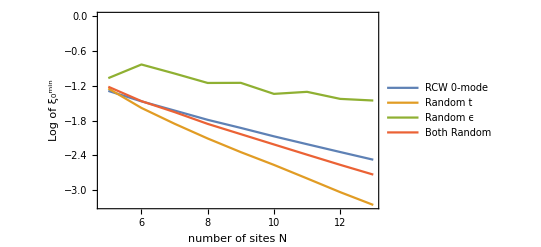

```mathematica
ListLinePlot[{Log10[mcn],Log10[man1],Log10[man],Log10[man2]},PlotRange->All,PlotLegends->{"RCW 0-mode","Random t","Random ϵ","Both Random"},Frame->True,FrameLabel->{"number of sites N","Log of ξ_0^min",Black},BaseStyle->{FontSize->15,FontWeight->"",FontColor->Darker[Black]} ,LabelStyle->Directive[Black]]
```

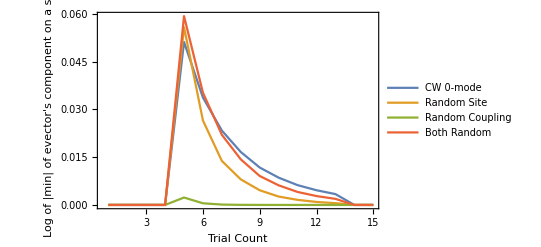

```mathematica
ListLinePlot[{mcn,man1,man,man2},PlotRange->All,PlotLegends->{"CW 0-mode","Random Site","Random Coupling","Both Random"},Frame->True,FrameLabel->{"Trial Count","Log of |min| of evector's component on a site"},InterpolationOrder->1]
```

```mathematica
mcn
```

{0,0,0,0,0.0379086,0.0241965,0.0159325,0.0107118,0.00747846,0.00528833,0.00391334,0.00280544,0.00205825,0,0}

```mathematica
r=10;a=1.0;q=5;
(* qt is q^∼ (Majorana mass term), and a is mass term (m) and q is Dirac mass term in cw fermions. *)
ce1[a_,q_]:=RandomReal[{-2a-2q,2q+2a},r] ;
ce2[a_,q_]:=RandomReal[{-a,a},r] ;
gc = ce1[a,q];
hc = ce1[a,q];
cw2 = Table[0,{x,2r+1},{y,2r+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;While[i<r+1,{cw2[[i,r+i]] = cw2[[r+i,i]] = 0+1.0*gc[[i]]};i++];
i=1;While[i<r+1,{cw2[[i,r+1+i]] =cw2[[r+1+i,i]] = -01.0*hc[[i]]};i++];
cw2;
cw3 = cw2[[r+1;;2r+1,1;;r]];
cw4=cw3.Transpose[cw3];
cw=cw3//Transpose;
```

```mathematica
uc=Eigenvectors[Transpose[cw].cw];
vc=Eigenvectors[cw.Transpose[cw]];
uc[[1]]
```

{-6.3816×10^-11,4.59731×10^-10,-2.82524×10^-9,-3.88247×10^-8,-0.0000225842,-0.140961,0.83008,0.522839,-0.124131,0.0474784,-0.00862745}

```mathematica
sc=Table[Min[Abs[uc[[i]]]],{i,1,11}]
sc2=Table[Min[Abs[vc[[i]]]],{i,1,10}]
```

{6.3816×10^-11,2.94048×10^-10,9.69755×10^-9,2.04923×10^-7,5.41165×10^-8,4.7925×10^-7,2.66364×10^-7,0.00254948,0.000123716,0.00763158,0.00563704}

{1.99241×10^-10,7.51466×10^-10,1.06663×10^-8,2.11058×10^-7,8.96783×10^-8,5.54516×10^-7,1.22018×10^-6,0.00354882,0.00013245,0.000287736}

```mathematica
nc=NullSpace[cw]
```

(0.0537789 | 0.044289 | 0.0885144 | -0.0207362 | 0.00563704 | -0.808185 | -0.326581 | 0.333138 | 0.175154 | 0.145648 | 0.253295)

```mathematica
Min[Abs[uc[[2]]]]
```

2.94048×10^-10

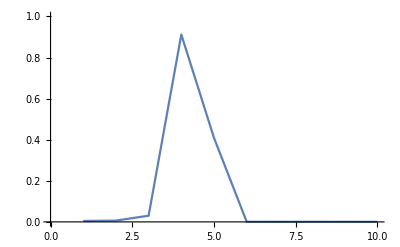

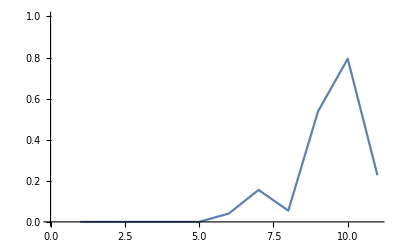

```mathematica
ListLinePlot[Abs[vc[[-1]]],PlotRange->{Automatic,{0,1}},PlotLegends->Automatic]
ListLinePlot[Abs[uc[[2]]],PlotRange->{Automatic,{0,1}},PlotLegends->Automatic]
```

```mathematica
ListLinePlot[Abs[sc[[-1]]],PlotRange->{Automatic,{0,1}},PlotLegends->Automatic]
ListLinePlot[Abs[uc[[2]]],PlotRange->{Automatic,{0,1}},PlotLegends->Automatic]
```

ListLinePlot::lpn: 0.00563704 is not a list of numbers or pairs of numbers.

ListLinePlot[0.00563704,PlotRange→{Automatic,{0,1}},PlotLegends→Automatic]

-Graphics-

```mathematica
ccw=Table[0,{i,4+7}];
```

```mathematica
i1=1;
While[i1<8,{r=4+i1;a=1.0;q=5;
cw2 = Table[0,{x,2r+1},{y,2r+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;While[i<r+1,{cw2[[i,r+i]] = cw2[[r+i,i]] = 1.0};i++];
i=1;While[i<r+1,{cw2[[i,r+1+i]] =cw2[[r+1+i,i]] =-5 };i++];
cw2;
cw3 = cw2[[r+1;;2r+1,1;;r]];
cw4=cw3.Transpose[cw3];
cw=cw3//Transpose;
nc=NullSpace[cw];
ccw[[4+i1]]=Min[Abs[nc[[1]]]]};i1++]
```

```mathematica
ccw=ccw*0.1
```

{0.,0.,0.,0.,0.0000313535,6.27069×10^-6,1.25414×10^-6,2.50828×10^-7,5.01655×10^-8,1.00331×10^-8,2.00662×10^-9}

```mathematica
ccw2=Table[0,{i,4+7}];
```

```mathematica
i1=1;
While[i1<8,{r=4+i1;a=1.0;q=5;
cw2 = Table[0,{x,2r+1},{y,2r+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;While[i<r+1,{cw2[[i,r+i]] = cw2[[r+i,i]] = 1.0};i++];
i=1;While[i<r+1,{cw2[[i,r+1+i]] =cw2[[r+1+i,i]] =-5-1*i};i++];
cw2;
cw3 = cw2[[r+1;;2r+1,1;;r]];
cw4=cw3.Transpose[cw3];
cw=cw3//Transpose;
nc=NullSpace[cw];
ccw2[[4+i1]]=Min[Abs[nc[[1]]]]};i1++]
```

```mathematica
ccw2=ccw2*0.1
```

{0.,0.,0.,0.,3.26097×10^-6,2.96452×10^-7,2.47043×10^-8,1.90033×10^-9,1.35738×10^-10,9.04921×10^-12,5.6557×10^-13}

```mathematica
aw=Table[0,{i,4+7}];
```

```mathematica
i2=1;
While[i2<8,{t=1;W=5;K=4+i2;
Ox = Table[0,{x,K},{y,K}]; 
i=1;While[i<K+1,{Ox[[i,i]] =002.0W };i++];
i=1;While[i<K,{Ox[[i+1,i]] =Ox[[i,i+1]] =t/2};i++];
{u,w,v} = SingularValueDecomposition[Ox]; 
(* We are taking the SVD decomposition for above defined mass matrix to convert it to a basis where Subscript[L, i] basis can be converted to Subscript[ψ, L]^i basis and Subscript[R, i] basis to Subscript[ψ, R]^i basis. *)
loke= Simplify[Inverse[Transpose[u]]];
(*This gives the conversion of Subscript[ψ, L]^i basis to Subscript[L, i] basis. Hence the components Subscript[v, 1]^n can be extracted from this matrix. *)
Roke = Simplify[Inverse[ConjugateTranspose[v]]];
(*This gives the conversion of Subscript[ψ, R]^i basis to Subscript[R, i] basis. Hence the components Subscript[v, N]^n can be extracted from this matrix.*)
v1=loke[[1]];
vN=Roke[[K]];
(* Subscript[v, 1]^n are stored as elements of v1 *)
M =  Table[0,{x,K+1},{y,K+1}] ;
i=1;
While[i<K+1,{M[[1+i,1+i]]=w[[i,i]]};i++];
i=1;While[i<K+1,{M[[1,1+i]]=0.1*v1[[i]],M[[1+i,1]]=0.1*vN[[i]]};i++];
{um,wm,vm}=SingularValueDecomposition[SetPrecision[M,25]];
aw[[4+i2]]=wm[[-1,-1]]};i2++]
```

```mathematica
aw
```

{0,0,0,0,6.312375736641715686698223×10^-9,3.164118041334708079153015×10^-10,1.58603406133769415749851×10^-11,7.95009682863345173271899×10^-13,3.985025712466858190015679×10^-14,1.997183355434379805980109×10^-15,9.991706496502332661677148×10^-17}

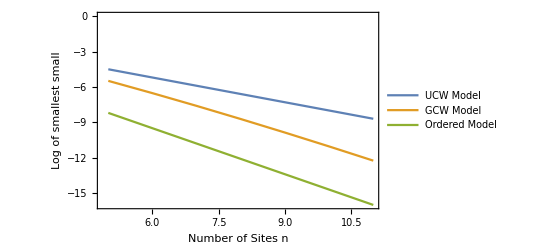

```mathematica
ListLinePlot[Log10[{ccw,ccw2,aw}],PlotRange->All,PlotLegends->{"UCW Model","GCW Model","Ordered Model"},Frame->True,FrameLabel->{"Number of Sites n","Log of smallest small"}]
```

## Section -2

```mathematica
s1 = 14;n=100;
```

```mathematica
cn=ParallelTable[r=s1;a=1.0;q=5;
(* qt is q^∼ (Majorana mass term), and a is mass term (m) and q is Dirac mass term in cw fermions. *)
ce1[a_,q_]:=RandomReal[{2a,2q+2a},r] ;
ce2[a_,q_]:=RandomReal[{-a,a},r] ;
gc = ce2[a,q];
hc = ce2[a,q];
cw2 = Table[0,{x,2r+1},{y,2r+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;While[i<r+1,{cw2[[i,r+i]] = cw2[[r+i,i]] = 0+1.0gc[[i]]};i++];
i=1;While[i<r+1,{cw2[[i,r+1+i]] =cw2[[r+1+i,i]] = -01.0hc[[i]]};i++];
cw2;
cw3 = cw2[[r+1;;2r+1,1;;r]];
cw4=cw3.Transpose[cw3];
cw=cw3//Transpose;
nc=NullSpace[cw];
Min[Abs[nc[[1]]]],{l,n}];
An=ParallelTable[e1[t_,W_]:=RandomReal[{2t,2t+2W},K] ;
e2[t_]:=RandomReal[{-t,t},K] ; (* Subscript[e, i] are randomly drawn from limit (2t , 2t+W) *)
t=1;W=5;K=s1; 
(* Attributing values for t , W and K . K is number of fermions. *)
g = e1[t,W];
h = e2[t];
Ox = Table[0,{x,K},{y,K}]; 
(* Defining the dummy matrix to store the values for mass matrix. *)
i=1;While[i<K+1,{Ox[[i,i]] =00.00W+1*g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i]] =Ox[[i,i+1]] =1t/2+00.0/2* h[[i]]};i++];
Ox;
Min[Abs[Eigenvectors[Ox][[-1]]]],{l,n}];
An1=ParallelTable[e1[t_,W_]:=RandomReal[{2t,2t+2W},K] ;
e2[t_]:=RandomReal[{-t,t},K] ; (* Subscript[e, i] are randomly drawn from limit (2t , 2t+W) *)
t=1;W=5;K=s1; 
(* Attributing values for t , W and K . K is number of fermions. *)
g = e1[t,W];
h = e2[t];
Ox = Table[0,{x,K},{y,K}]; 
(* Defining the dummy matrix to store the values for mass matrix. *)
i=1;While[i<K+1,{Ox[[i,i]] =01.00W+0*g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i]] =Ox[[i,i+1]] =0t/2+01* h[[i]]};i++];
Ox;
Min[Abs[Eigenvectors[Ox][[-1]]]],{l,n}];
An2=ParallelTable[e1[t_,W_]:=RandomReal[{2t,2t+2W},K] ;
e2[t_]:=RandomReal[{-t,t},K] ; (* Subscript[e, i] are randomly drawn from limit (2t , 2t+W) *)
t=1;W=5;K=s1; 
(* Attributing values for t , W and K . K is number of fermions. *)
g = e1[t,W];
h = e2[t];
Ox = Table[0,{x,K},{y,K}]; 
(* Defining the dummy matrix to store the values for mass matrix. *)
i=1;While[i<K+1,{Ox[[i,i]] =00.00W+1*g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i]] =Ox[[i,i+1]] =0t/2+01* h[[i]]};i++];
Ox;
Min[Abs[Eigenvectors[Ox][[-1]]]],{l,n}];
```

```mathematica
Median[cn]
```

0.00170891

```mathematica
Median[An]
```

1.95811×10^-9

```mathematica
Median[An1]
```

0.0000635619

```mathematica
Median[An2]
```

4.59779×10^-11